amplitude

707

zero - 1200Hz

58

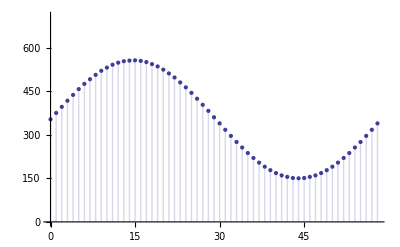

one - 2200Hz

31

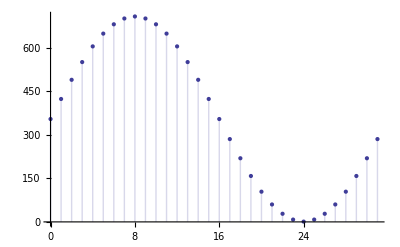

zero - 1200Hz

(353.
375.
396.
417.
437.
457.
475.
491.
506.
520.
531.
541.
548.
553.
555.
556.
554.
550.
543.
535.
524.
511.
497.
480.
463.
444.
424.
403.
382.
360.
339.
317.
296.
275.
256.
237.
220.
204.
190.
178.
168.
160.
155.
151.
150.
151.
155.
160.
168.
178.
190.
204.
220.
237.
256.
275.
296.
317.
339.)

one - 2200Hz

(354.
423.
489.
550.
604.
648.
680.
700.
707.
700.
680.
648.
604.
550.
489.
423.
354.
285.
219.
158.
104.
60.
28.
8.
1.
8.
28.
60.
104.
158.
219.
285.)

```mathematica
Clear["Global`*"]
samples:=32
amplitude:=707
halfAmplitude:=((amplitude-1)/2)
period1:=(2π)/samples
samplesCount1:=Round[(2π)/period1]-1
period0:=1200/2200 period1
samplesCount0:=Floor[(2π)/period0]
(* added pre-emphasis *)
f0[x_]:=Round[150+(halfAmplitude-150)(1+Sin[period0*x])]
f1[x_]:=Round[1+halfAmplitude(1+Sin[period1*x])]

"amplitude"
Round[amplitude]
"zero - 1200Hz"
samplesCount0
DiscretePlot[f0[x],{x,0,samplesCount0},PlotRange->{{0,samplesCount0},{0,amplitude}}]
"one - 2200Hz"
samplesCount1
DiscretePlot[f1[x],{x,0,samplesCount1},PlotRange->{{0,samplesCount1},{0,amplitude}}]
"zero - 1200Hz"
MatrixForm[Table[N[f0[x]],{x,0,samplesCount0,1}]]
"one - 2200Hz"
MatrixForm[Table[N[f1[x]],{x,0,samplesCount1,1}]]
```